# Machine Learning Classify

Classify takes a dataset and learns from it. Then given a value it predicts its label. Classify can be used on many types of data, including numerical, textual, sounds, and images, as well as combinations of these. Classify[training] returns a ClassifierFunction[…] that can then be applied to specific data. Depending on the dataset, it decides which algorithm to choose.
First try on a very small dataset.

```mathematica
c=Classify[{1->"A",2->"B",3->"C",4->"D",5->"F",6->"H"}]
```

ClassifierFunction[…]

```mathematica
c[2]
```

B

```mathematica
c[2.5]
```

B

```mathematica
c[7]
```

H

```mathematica
c[66]
```

H

```mathematica
c[5.3]
```

H

```mathematica
c[4.1]
```

H

```mathematica
c[3,"Probabilities"]
```

<|A→0.222222,B→0.222222,C→0.222222,D→0.111111,F→0.111111,H→0.111111|>

Plotting the probabilities for A.

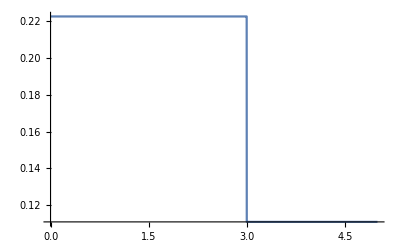

```mathematica
Plot[c[x,{"Probability","A"}],{x,0,5},Exclusions->None]
```

Classify on the famous cats-vs-dogs problem.

```mathematica
set = <|"cat"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},"dog"->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>;
```

```mathematica
c = Classify[set]
```

ClassifierFunction[…]

```mathematica
c[-Graphics-]
```

cat

```mathematica
c[-Graphics-,"Probabilities"]
```

<|cat→9.88303×10^-52,dog→1.|>

```mathematica
c[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

```mathematica
{"dog","cat","cat","dog","dog"} (*pretty much correct*)
```

```mathematica
c[-Graphics-,"Probabilities"]
```

<|cat→1.,dog→8.15162×10^-36|>

Looking for accuracy and ConfusionMatrix for the given classifier.

```mathematica
cm = ClassifierMeasurements[c,{-Graphics-->"dog",-Graphics-->"cat",-Graphics-->"dog",-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"dog",-Graphics-->"dog",-Graphics-->"cat",-Graphics-->"cat"}]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.888889

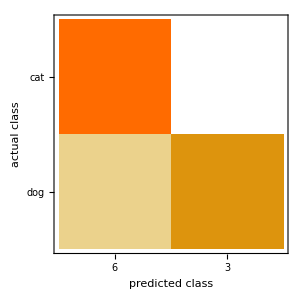

```mathematica
cm["ConfusionMatrixPlot"]
```

General built-in classify functions, can classify flags, language, person etc.

```mathematica
Classify["NotablePerson",Entity["Person","AlbertEinstein::6tb7g"][EntityProperty["Person","Image"]],{"TopProbabilities",3}]
```

{Charles Dickens→0.24042,Robert E. Lee→0.137042,Albert Einstein→0.10268}

```mathematica
Classify["CountryFlag",Entity["Country","India"]["FlagImage"],{"TopProbabilities",3}]
```

{India→0.909483,Zimbabwe→0.00039185,Zambia→0.00039185}

```mathematica
Classify["Language","nimeni on khushmeet Singh.
Olen tietojenkäsittelytieteen opiskelija vit yliopistossa Intiassa",{"TopProbabilities",5}]
```

{Finnish→1.,Estonian→1.3495×10^-11,Bokmål Norwegian→8.60528×10^-16,Swedish→4.38464×10^-16,Esperanto→1.20426×10^-16}

```mathematica
Classify["NameGender","Khushmeet",{"TopProbabilities",5}]
```

{Female→0.5,Male→0.5}

```mathematica
Classify["Profanity","this shit is dope",{"TopProbabilities",5}]
```

{True→1.,False→0.}

```mathematica
Classify["Sentiment","As a background, I am a retired Information Systems professional and I am writing this review from the perspective of being a long-time Kindle user. I have all the current e-readers and Fire devices from Amazon including the basic Kindle, the 2013, 2014 and new 2015 Paperwhite, the Fire HD6, Fire HD7, Fire HDX7 and Fire HDX8.9. This review is for the 2015 “All-New Kindle Paperwhite.” The attached picture shows the 2014 Kindle on the left and the new 2015 Kindle on the right. Here is the summary of my initial impressions of the 2015 model versus the 2014 model.

I am somewhat disappointed in the 2015 version as there is not a huge improvement over last year’s model. The Paperwhite made many improvements from its original first generation 2012 model to its second generation 2013 model, especially in the display and processor area. The 2013 model came with 2 GB storage, a wonderful display, a great battery and was the e-book “workhorse.” The second generation 2014 model changed by only increasing storage to 4 GB. The third generation 2015 model increased the display resolution but reduced the battery life slightly.

WHAT COMES IN THE BOX: A Paperwhite device, a quick-start guide and a short USB cord. Amazon still does not supply a power adapter.

SIZE: It’s the same identical size as the older Paperwhites. The weight has been reduced slightly from 7.3 to 7.2 ounces, a fraction of an ounce, most likely because of a smaller battery.
The good news is that all cases that fit the other Paperwhites will fit the 2015 version!!",{"TopProbabilities",2}]
```

{Neutral→0.994323,Negative→0.00567671}